```mathematica
dwarfNum = 20; raBins = 36; decBins = 36;
SetDirectory[NotebookDirectory[]];
BrownData = Import["UltracoolSheetMain.csv"];
headers = First[BrownData]; rows = Rest[BrownData];
(*This beginning part is seperating the header row from the rest of the data we import*)

smallBrownData=rows[[All,{First@First@Position[headers,"name"],First@First@Position[headers,"name_simbadable"],First@First@Position[headers,"ra_j2000_formula"],First@First@Position[headers,"dec_j2000_formula"]}]]
(*This code is taking only the columns with the header names as the strings and making a smaller list with only those 4 headers*)
```

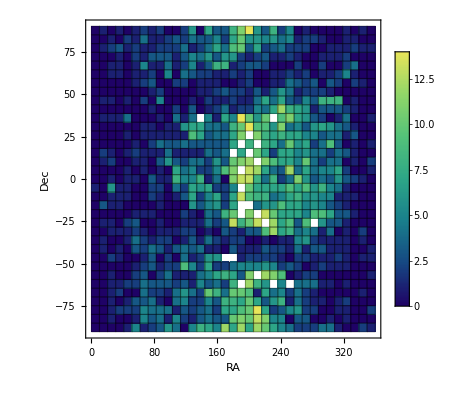

```mathematica
pts = smallBrownData[[All, {3, 4}]];
binSizeRA = 360/36;binSizeDec = 180/36;
RAEdge = Range[0,360, binSizeRA];
DecEdge = Range[-90,90, binSizeDec];
counts = BinCounts[pts, {RAEdge}, {DecEdge}];
CoolColor[ z_ ] :=RGBColor[z,1-z,1];

(*This code above is taking just the RA and Dec parts of our data and assigning it to points, then we choose to break up the celestial sphere into a square with 36 X 36 squares across to find where the stars are most prevelant*)
(*The counts variable uses BinCounts to count up how many BrownDwarfs appear in each square*)

ListDensityPlot[counts, DataRange -> {{0,360},{-90,90}}, FrameLabel-> {"RA", "Dec"}, PlotLegends -> Automatic, ColorFunction ->"BlueGreenYellow",Mesh -> All, InterpolationOrder -> 0]


(*This Plot shows where the Brown Dwarf Stars are concentrated with the dark blue representing low concentration and the light green/yellow being high*)
```

```mathematica
binsdata = BinLists[pts, {RAEdge}, {DecEdge}];
lookup=Association[({#[[3]],#[[4]]}->#[[1]])&/@smallBrownData];
Map[Append[#,lookup[{#[[1]],#[[2]]}]]&,binsdata,{3}]
(* Using the pts, RAEdge, DecEdge, and smallBrownData from above, this code creates a list of lists in which each sublist is a bin of data, and it consists of the declinations, right ascensions, and names of each star in that bin.*)
```

```mathematica
raBins=36;
decBins=36;

raEdges=Range[0,360,360/raBins];
decEdges=Range[-90,90,180/decBins];

k=1;

(*Do[raMin=raEdges[[j]];
raMax=raEdges[[j+1]];
decMin=decEdges[[i]];
decMax=decEdges[[i+1]];
currentChunk=Select[smallBrownData,raMin<=#[[3]]<raMax&&decMin<=#[[4]]<decMax&];
If[Length[currentChunk]>=1,Export["UltracoolChunk"<>ToString[k]<>".csv",Prepend[currentChunk,{"name","name_simbadable","raj2000","decj2000"}]];
k++;],{i,Length[decEdges]-1},{j,Length[raEdges]-1}]*)

(*This code will take the ultracoolsheet and split it up into chunks of about 20 stars so that you can take it to a spectrophotometry tool and pull data*)
```

```mathematica
plotspec[]:=Module[{Bd,Bd2,BdSpect,BdSpect2,x,y,x2,y2,plot1,plot2},Bd=Input["input JSON Brown Dwarf Spectrum"];
Bd2=Input["input a second JSON Brown Dwarf Spectrum"];
BdSpect=Import[Bd,"RawJSON"];
x=BdSpect["data"][[1,"x"]];
y=BdSpect["data"][[1,"y"]];
BdSpect2=Import[Bd2,"RawJSON"];
x2=BdSpect2["data"][[1,"x"]];
y2=BdSpect2["data"][[1,"y"]];
plot1=ListLinePlot[Transpose[{x,y}],Frame->{{True,False},{True,True}},FrameLabel->{{"Microjanskys (µJy)",None},{"Micrometers (µm)",None}},PlotStyle->Blue,ImagePadding->40];
plot2=ListLinePlot[Transpose[{x2,y2}],Frame->{{False,True},{False,False}},FrameTicks->{{None,Automatic},{None,None}},FrameLabel->{{None,"Microjanskys (µJy)"},{None,None}},PlotStyle->Red,Axes->False,Background->None,ImagePadding->40];
Overlay[{plot1,plot2}]]
```

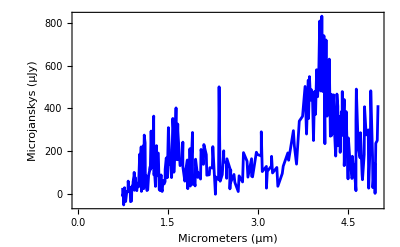
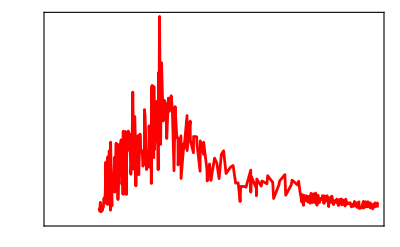

```mathematica
plotspec[]
(*This module function will take 2 json files containing spectrophotometry data and overlay both so that you will be able to compare them*)
```